```mathematica
m:={0,4.7,9.5,14.3,19.1,23.9,28.7,0,4.7,9.5,14.3,19.1,24.0,28.7};
L:={4.88,6.92,8.99,11.09,13.18,15.26,17.39,4.95,7.00,9.10,11.20,13.30,15.41,17.51};
data:=Table[{m[[i]],L[[i]]},{i,1,14}]
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[4.90738+0.436293 x]

```mathematica
model["BestFit"]
```

4.90738+0.436293 x

```mathematica
model[1]
```

5.34367

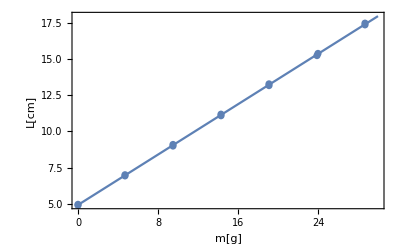

```mathematica
Show[Plot[model["BestFit"],{x,0,30},
Frame->{True,True,False,False},
FrameTicks->{{Automatic, None},{Automatic,None}},
FrameLabel->{"m[g]","L[cm]"}],ListPlot[data]]
```

```mathematica
Sum[(L[[i]]-Mean[L])^2,{i,1,14}]
```

244.912

```mathematica
rr=(244.912-Sum[(L[[i]]-model[m[[i]]])^2,{i,1,14}])/244.912
```

0.999837

```mathematica
sse=Sum[(L[[i]]-model[m[[i]]])^2,{i,1,14}]
```

0.0398547

```mathematica
rr Sqrt[12]/Sqrt[1-rr^2]
```

191.994

```mathematica
0.039854694049338425-0.0322
```

0.00765469